```mathematica
TeXForm[HoldForm[Integrate[f[θ],{θ,-π,π}]]]
```

\int_{-\pi }^{\pi } f(\theta ) \, d\theta

```mathematica
ToExpression["\\int_{-\\pi }^{\\pi } f(\\theta) \\, d\\theta",TeXForm,Hold]
```

Hold[∫_-π^π f[θ]ⅆθ]

```mathematica
DSolve[y''[x]/y[x]-2(y'[x]/y[x])^2==1,y[x],x]
```

{{y[x]→C[2] Sec[x+C[1]]}}

```mathematica
D[1/b[η],{η,2}]/(1/b[η])==D[1/a[η],{η,2}]/(1/a[η])+k
%/.{a->Function[η,Sec[η]],k->1}//FullSimplify
Inactive[DSolve][%,b,η]
Activate[%]
```

b[η] ((2 b'[η]^2)/b[η]^3-b''[η]/b[η]^2)==k+a[η] ((2 a'[η]^2)/a[η]^3-a''[η]/a[η]^2)

b''[η]==(2 b'[η]^2)/b[η]

DSolve[b''[η]==(2 b'[η]^2)/b[η],b,η]

{{b→Function[{η},C[2]/(η+C[1])]}}

```mathematica
B/(η+A)
%/.{B->1255.765989664208 (1.57+A)}
Solve[Limit[D[%,η]/D[Sec[η],η],η->1.57]==1,A]
```

B/(A+η)

(1255.77 (1.57+A))/(A+η)

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
{{A->-1.5707963269632232}}
```

```mathematica
1255.765989664208 (1.57+A)
%/.{A->-1.5707963269632232}
```

1255.77 (1.57+A)

-1.

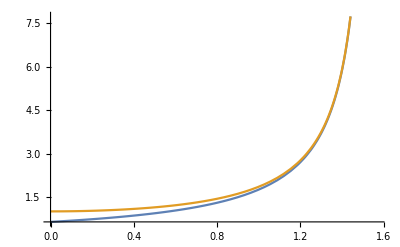

```mathematica
Plot[{-1/(η-1.5707963269632232),Sec[η]},{η,0,π/2}]
```